# Analiza danych SD

## Definicje ścieżek i tworzenie katalogów

```mathematica
pathFigs="./figs/"
```

./figs/

```mathematica
If[!DirectoryQ[pathFigs],CreateDirectory[pathFigs]]
```

## Przykładowe rozkłady

```mathematica
g1=RandomGraph@BarabasiAlbertGraphDistribution[10^3,1];
g2=RandomGraph@BarabasiAlbertGraphDistribution[10^3,2];
```

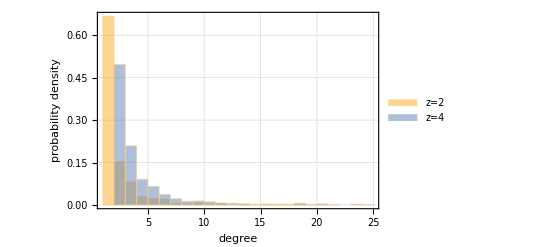

```mathematica
fig=Histogram[
{VertexDegree[g1],VertexDegree[g2]},
{1,25,1},"PDF",Frame->True,ChartLegends->{"z=2","z=4"},GridLines->Automatic,FrameLabel->{"degree","probability density"}]
```

```mathematica
Export[pathFigs<>"dist.pdf",fig]
```

./figs/dist.pdf

## Init

```mathematica
SetDirectory[NotebookDirectory[]];
```